## LCA over een rechthoek

Beschouw een rechthoek met breedte W en lengte L zoals onderstaande figuur. De golfvergelijking λ Φ = -Ω^2 ∇^2 Φ kan hierover numeriek worden opgelost. Met behulp van NDEigensystem worden deze oplossingen samen met hun eigenwaarden berekend. De eigenwaarden komen overeen met die voor de ribbon met k = (m π)/L met m een natuurlijk getal.

Voor de eigenfuncties gevonden door NDEigensystem geldt:
 -Graphics-

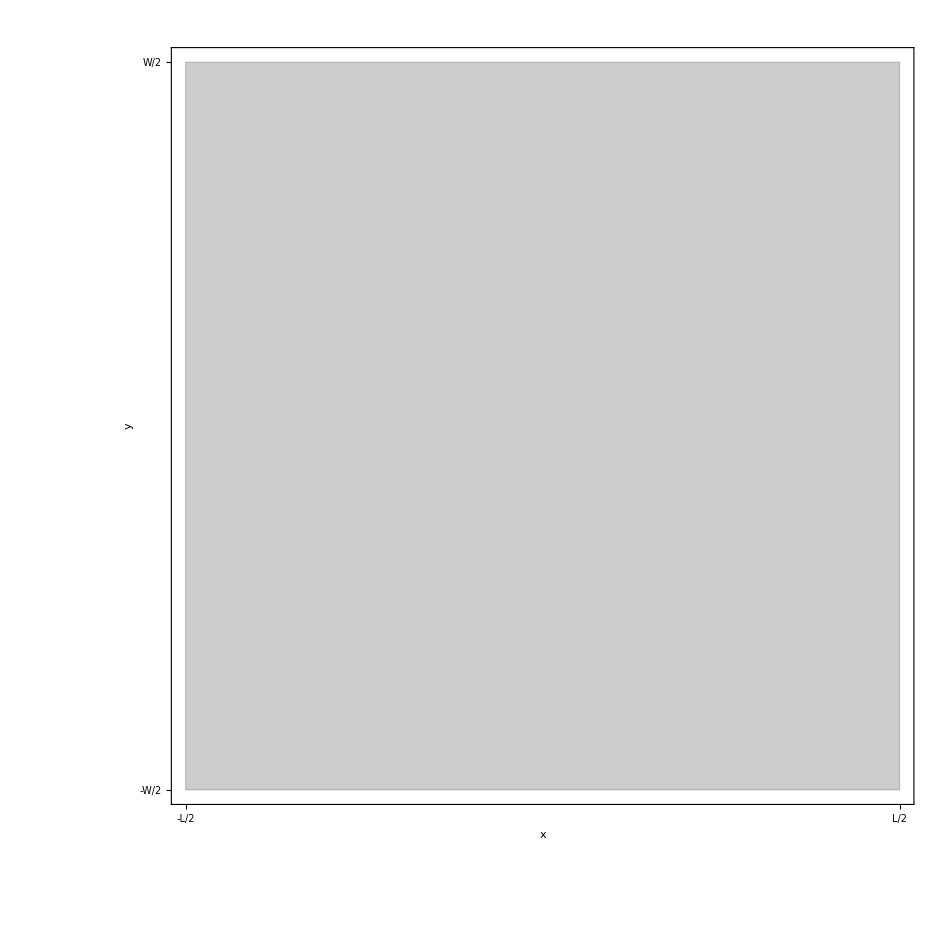

{{1.03621×10^-15,0.0986961,0.0986961,0.197392,0.394789,0.394789,0.493486,0.493486,0.789579,0.888325},{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}}

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Ω = 1/Sqrt[2π];
L = 10;
W=10;
n = 10;
Graphics[{EdgeForm[Thin],Opacity[0.2],Rectangle[{-L/2,-W / 2},{L/2,W / 2}]}, Frame->True,FrameTicks->{{{{-W/2, "-W/2"},{W/2, "W/2"}},None},{{{-L/2,"-L/2"},{L/2,"L/2"} },None}},Axes->True, AxesLabel->{x,y}, PlotRange->Automatic]

{vals,funs}=NDEigensystem[{- ( Derivative[0,2][u][x,y]+Derivative[2,0][u][x,y])+NeumannValue[0,x ==  L/2]+NeumannValue[0,y==W / 2]+NeumannValue[0,x==-L/2]+NeumannValue[0,y==-W / 2]},u,{x,y}∈Rectangle[{-L/2,-W / 2},{L/2,W / 2}],n]
Table[Plot3D[funs[[i]][x,y],{x,-L/2,L/2},{y, -W/2,W/2},PlotRange->All,PlotLabel->StringForm["λ = ``", Re[Sqrt[vals[[i]]]]], AxesLabel->{Text[Style["x",FontSize->12]],Text[Style["y",FontSize->12]], Text[Style["Φ",FontSize->12]]}],{i,Length[vals]}]
```

## Berekenen van de eigenwaarden voor de Coulomb potentiaal

Wat ik verwacht is de kleinste eigenwaarden op de grafiek voor de ribon met Coulomb voor alle k=nπ/L met n een natuurlijk getal.

```mathematica
Monitor[Lm = ParallelTable[ Ω^2  NIntegrate[(funs[[i]][x1,y1]funs[[j]][x2,y2])/Sqrt[(x1-x2)^2+(y1-y2)^2+ (0.0001)^2],{x1,-L/2,L/2},{y1, -W/2,W/2}, {x2,-L/2,L/2},{y2, -W/2,W/2}, PrecisionGoal->4,AccuracyGoal->4, Method->{"GlobalAdaptive"},MinRecursion->8,MaxRecursion->30], {i,1,n},{j,1,n}],{i,j}]
Pm = Table[KroneckerDelta[i,j] vals[[i]], {i,1,n},{j,1,n}];
mat = Pm . Lm;
Eigenvalues[mat]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.283508 and 4.50992 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0108094 and 2.62778 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0449796 and 2.10554 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0393988 and 1.87386 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.324566 and 1.87471 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 30.9085 and 1.68277 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0488155 and 2.66177 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.966107 and 2.87432 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00318029 and 1.70644 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00815519 and 2.48139 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.787196 and 2.27353 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0393988 and 1.87386 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.649103 and 2.82708 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0217282 and 2.36629 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00560974 and 2.38662 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.04823 and 2.74092 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 13.3249 and 1.94629 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0393988 and 1.87386 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{{4.91924,0.00627052,-0.00627052,-0.0000450623,-0.0516563,0.532352,0.00715872,-0.00715872,0.0451216,-0.00172037},{0.00627052,2.12073,0.000506158,0.00031779,-0.00129794,0.00946166,0.125286,-0.166832,-0.00776923,-0.153761},{-0.00627052,0.000506158,2.12073,-0.00031779,0.000892817,-8.13426×10^-6,-0.166832,-0.125286,-0.00345816,0.103308},{-0.0000450623,0.00031779,-0.00031779,1.52555,-0.000132538,0.0000879229,-0.0006997,0.0006997,0.00997297,0.00560542},{-0.0516563,-0.00129794,0.000892817,-0.000132538,1.33909,-0.0115708,-0.00647498,-0.00106232,-0.0155569,-0.00109236},{0.532352,0.00946166,-8.13426×10^-6,0.0000879229,-0.0115708,1.43119,0.00108873,0.00009595,0.168799,0.0000161876},{0.00715872,0.125286,-0.166832,-0.0006997,-0.00647498,0.00108873,1.2779,-0.00134593,0.00167284,0.00716743},{-0.00715872,-0.166832,-0.125286,0.0006997,-0.00106232,0.00009595,-0.00134593,1.2779,-0.00581416,0.0186961},{0.0451216,-0.00776923,-0.00345816,0.00997297,-0.0155569,0.168799,0.00167284,-0.00581416,1.23282,-0.000172491},{-0.00172037,-0.153761,0.103308,0.00560542,-0.00109236,0.0000161876,0.00716743,0.0186961,-0.000172491,1.06613}}

{0.994366,0.951707,0.635998,0.634609,0.544741,0.527979,0.3011,0.204363,0.200287,4.88498×10^-15}

```mathematica
Ordering[Abs[Eigenvectors[mat][[1]]],-1]
```

{10}

```mathematica
Eigenvalues[Pm . Lm]
```

{67.0154,-62.522,29.064,-23.3779,8.78027,-6.24352,4.2348,3.46978,2.75269,2.60095,2.48817,2.20145,2.18313,1.26115,0.963503,0.817506,0.34006,0.232235,0.073114,-2.06755×10^-14}

```mathematica
Eigenvectors[mat][[2]]
```

{-1.41425×10^-18,0.000176059,-0.0000185798,0.347662,0.0000253116,0.0019841,0.000171638,0.0764006,-0.000416918,-0.9345}

```mathematica
n
```

## Eigenfuncties

```mathematica
eigvectors = Eigenvectors[Pm . Lm]
```

{{1.44106×10^-14,0.0000227758,-0.000245662,0.217385,0.000364565,0.000246392,0.00611003,-0.000253839,0.00191159,0.00177581,0.00108937,-0.00299755,-0.975162,-0.0039073,0.00628165,-0.00896828,0.00760018,0.00394936,-0.00961629,0.0380447},{2.34686×10^-14,0.0000388185,0.000239441,-0.26994,-0.000468147,0.000139812,-0.00352719,-0.000334454,-0.00201526,-0.00146125,-0.000884718,-0.00777283,-0.962669,-0.00315212,-0.00405034,-0.00559928,-0.00420255,0.00553531,0.00416693,0.0140257},{-2.2788×10^-16,0.0000146402,-0.0000403089,-0.00209905,-0.000225396,-0.000417769,0.186186,-0.00127241,-0.000406459,0.00629348,-0.00142241,0.000927801,0.0127396,0.0206941,-0.0149865,-0.0702477,-0.00119123,0.0404926,0.00747901,0.978693},{9.83363×10^-17,-4.77131×10^-6,-0.000223564,0.000839062,0.0013004,-0.0000802727,-0.00081242,0.000233311,0.00195003,-0.00124097,-0.00218252,0.00420759,-0.00166689,-0.000109589,-0.183183,-0.0235654,0.13434,0.00803687,0.973407,-0.0149278},{7.30947×10^-16,-7.16311×10^-6,-0.00124939,0.000949792,0.00138021,-0.0000491088,-0.000996802,0.000249337,0.0181796,-0.00174983,0.0118696,0.00138379,-0.00140999,-0.00587719,-0.00410427,-0.0353219,-0.984216,0.0356844,0.167982,-0.00673997},{-2.61418×10^-17,-0.000145211,0.000131352,0.0000274553,0.000178763,0.00106812,-0.0249601,-0.0154069,-0.00204033,-0.0301617,0.000386623,0.0192191,0.00433434,-0.0813338,0.0167853,-0.619796,0.0477632,0.774379,-0.0374415,-0.0587039},{-1.07312×10^-16,-0.000413197,-0.000101015,-0.000315967,0.000186812,-0.0118611,-0.00150847,0.0134328,0.00114002,-0.0353079,0.0085139,0.00914163,0.00275462,-0.530591,0.0775162,-0.534996,0.00780462,-0.65149,-0.0017922,0.00205783},{4.18529×10^-16,-0.0000282054,0.000364658,0.000729688,0.00157829,-0.000159065,0.0065099,0.000275298,0.00359659,-0.00831408,0.000154865,-0.0040632,-0.000889525,-0.0529535,-0.953167,-0.0166985,-0.0327144,-0.00884948,-0.292974,-0.0355246},{1.17283×10^-17,0.000195116,0.000113509,0.000020343,0.000276868,-0.0138477,-0.0220336,0.00536481,-0.0021632,0.0278198,0.0040813,-0.0182059,-0.00102421,0.717624,-0.0225513,-0.543215,-0.00132528,-0.431825,-0.0100845,-0.0318579},{2.64768×10^-16,0.000306648,-0.00142351,0.000695187,0.00014628,0.0380927,-0.000177999,0.049983,0.0151742,0.020427,-0.00835346,-0.996002,0.00659607,-0.0345928,0.00659964,-0.0247639,0.00199761,0.0357613,0.0114719,0.0000657952},{-4.37783×10^-16,0.0000200848,0.00745971,-0.000275631,-0.00455017,0.000782074,-0.0000284274,-0.0065127,-0.0737427,0.014666,0.996478,-0.0128118,0.000409895,0.00190415,-0.00257896,0.0149166,0.0247958,0.0141555,0.00406696,0.00547085},{9.13502×10^-16,0.000102785,0.00071061,-0.00125743,0.00168959,0.000156679,0.460135,-0.00103797,0.00180454,0.0132542,0.00151604,0.000476237,-0.00623327,0.0233372,0.0340366,-0.0527802,0.00322641,0.0157114,-0.000500327,-0.885044},{3.14874×10^-16,0.000968045,0.000475312,0.000679203,0.00112664,-0.0174814,0.0142577,0.0788718,-0.00416249,-0.986734,0.0176814,-0.0279925,-0.00107679,0.109954,0.0126708,0.0743483,0.00106672,-0.0260073,0.000259178,0.00727471},{3.33452×10^-15,-6.52597×10^-6,0.121954,0.00153716,0.0126855,0.000593114,0.000314247,0.0054715,-0.978735,0.00496538,-0.135172,-0.0310037,-0.00051389,-0.0107575,-0.00960429,0.000437243,-0.083147,-0.00431586,0.0246263,-0.00279061},{6.96577×10^-17,0.000479983,0.000413766,0.000222068,0.000141801,-0.00958157,0.00079342,-0.977381,-0.00332511,-0.125134,-0.0120637,-0.128466,0.00124628,-0.0012249,0.00205228,0.0135422,-0.00497746,-0.109888,0.00500924,0.000220753},{2.42479×10^-16,-0.000888817,-0.000425243,0.000191765,0.000521803,-0.968077,0.000908437,0.0208287,0.00107846,0.0614025,-0.000697274,-0.173165,-0.000126978,-0.0347378,0.00051441,0.0991926,0.000761612,0.132542,0.00328749,-0.00261628},{-7.0979×10^-15,6.0237×10^-7,-0.00517186,-0.0010845,0.997687,0.000989011,-0.00533852,-0.000523035,0.0377013,0.00608042,0.033458,0.00229831,0.000169623,0.000719663,0.0234702,0.00765352,0.022954,0.00120197,-0.0234837,0.0170253},{-4.64759×10^-15,0.0000272731,-0.448916,0.0000507723,-0.000682711,0.00108274,0.00570422,0.000453973,-0.89253,0.0000828631,-0.0189674,-0.0058829,7.13882×10^-6,-0.00418468,-0.0171022,0.000651982,-0.0299619,-0.00155607,0.00165416,-0.0149123},{-1.28936×10^-14,0.99053,0.000197513,0.000227814,-0.000060335,-0.0228101,-0.00782258,0.0163845,0.000236082,0.0750494,-0.00217422,0.0398342,0.00467884,-0.088145,-0.00130689,-0.0536364,0.000450925,-0.00870536,-0.00131361,0.00541031},{0.52344,0.00396836,-0.0169126,0.0527389,0.0341899,0.00140167,-0.0133598,-0.000120385,0.032117,0.00780955,0.0207667,0.017169,0.845116,-0.0000447816,0.0262746,0.0048768,0.0608058,-0.0080931,-0.0119531,0.0303023}}

```mathematica
Sum[Part[eigvectors,5,(i)]^2  , {i,1,n}]
```

1.

```mathematica
L
```

10

```mathematica
Table[Plot3D[Sum[Part[eigvectors,n-l,(i)] funs[[i]][ x,y] , {i,1,n}],{x,y}∈Rectangle[{-L/2,-W / 2},{L/2,W / 2}], PlotRange->Full],{l,0,n-1}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Plot3D[funs[[7]][x,y],{x,y}∈Rectangle[{-L/2,-W / 2},{L/2,W / 2}]]
```

-Graphics3D-

```mathematica
L
```

1

```mathematica
Export["RechthoekL100eigenvectoren.csv", eigvectors, "CSV"]
```

RechthoekL100eigenvectoren.csv